## Graphical representation for the reduced inertia parameter defined in Frauendorf paper

```mathematica
ClearAll["Global`*"]
```

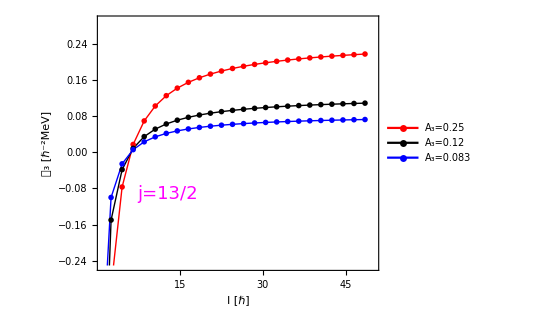

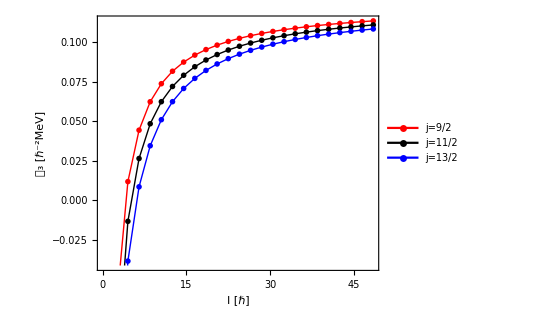

```mathematica
realspin[I_]:=Sqrt[I(I+1)];
A3reduced[A3_,I_,j_]:=A3*(1-j/realspin[I]);
plotdata[A3_,j_]:=Table[{spin,A3reduced[A3,spin,j]},{spin,1/2,50,2}];
makeplotfixedj[I3list_,j_]:=ListPlot[Table[plotdata[1/(2*I3list[[i]]),j],{i,1,Length[I3list]}],Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,FrameLabel->{"I [ℏ]","𝒜_3 [ℏ^-2MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},ImageSize->400,PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},PlotMarkers->"OpenMarkers",GridLines->{{{j,Directive[Magenta,Thick,Opacity[1],Dashed]}},Table[{1/(2I3list[[i]]),Directive[Thin,Opacity[1],Dashed,Black]},{i,1,Length[I3list]}]},PlotRange->{{1,50},{-0.25,0.29}},Epilog->{ Inset[Style[StringTemplate["j=(``)/2"][IntegerPart[2j]],Magenta,Italic,18]
,Scaled[{0.25,0.3}]]},PlotLegends->Placed[Table[StringTemplate["A_3=``"][N[1/(2*I3list[[i]]),2]],{i,1,Length[I3list]}],{0.8,0.25}]];
makeplotfixedI3[I3_,jlist_]:=ListPlot[Table[plotdata[1/(2*I3),jlist[[i]]],{i,1,Length[jlist]}],Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,FrameLabel->{"I [ℏ]","𝒜_3 [ℏ^-2MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},ImageSize->400,PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},PlotMarkers->"OpenMarkers",PlotRange->Automatic,PlotLegends->Placed[Table[StringTemplate["j=(``)/2"][IntegerPart[2jlist[[i]]]],{i,1,Length[jlist]}],{0.8,0.6}]];
fig1=makeplotfixedj[{2,4,6},6.5];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/odd-A-QTR-Model/reducedInertia_fig1.pdf",fig1,ImageResolution->1200];
Show[fig1]
fig2=makeplotfixedI3[4,{4.5,5.5,6.5}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/odd-A-QTR-Model/reducedInertia_fig2.pdf",fig2,ImageResolution->1200];
Show[fig2]
```